## Akshay Jaggi and Raymond Yuan Bessel Eigenvalue Investigation

The Bessel function differential equation can be linearized using the change of variables represented below.

Initial Equation:

```mathematica
t^2*x''[t]+t*x'[t]+(t^2-p^2)x[t]==0
```

(-p^2+t^2) x[t]+t x'[t]+t^2 x''[t]==0

Set x’[t]=y[t] and x’’[t] = y’[t]. This first definition gives the function x’[t], which is very useful later on, so we’ll save it as the function f.

```mathematica
f=y[t]
```

y[t]

```mathematica
t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0
```

(-p^2+t^2) x[t]+t y[t]+t^2 y'[t]==0

In order to obtain an equation for y’[t], we’ll use Solve.

```mathematica
g=y'[t]/.Solve[t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0,y'[t]][[1]]
```

(p^2 x[t]-t^2 x[t]-t y[t])/t^2

Now, the equilibrium point of the f, g system can be found using a quick replace all.

```mathematica
Solve[{f==0,g==0}/.{x[t]->x,y[t]->y},{x,y}]
```

{{x→0,y→0}}

The coefficient matrix of the system can then be used to find the eigenvalues. In the case of the bessel function system, the eigenvalues are time depedent. This indicates that the function’s behavior near (0,0) varies over time.

```mathematica
co={{0,1},{(p^2-t^2)/t^2,-1/t}}
```

{{0,1},{(p^2-t^2)/t^2,-1/t}}

```mathematica
Eigenvalues[co]
```

{(-t-t √(1+4 p^2-4 t^2))/(2 t^2),(-t+t √(1+4 p^2-4 t^2))/(2 t^2)}

```mathematica
Manipulate[StreamPlot[{f,g}/.{x[t]->x,y[t]->y,t->d,p->0},{x,-5,5},{y,-5,5}, PlotLabel->Evaluate[Eigenvalues[co]/.{t->d,p->0}//N]],{d,10^-9,20}]
```

Interestingly, the Eigenvalues are a saddle node for t=0, a sink for 0<t<=0.5, a spiral sink for 0.5<t<=10. For t>10, the function begins behaving much like a center as the real component of the eigenvalues approach zero.

Let’s apply this to a specific solution with p=0 and the initial speed zero and position 1.

```mathematica
DSolve[{t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0,y[t]==x'[t]},{x[t],y[t]},t]
```

{{x[t]→BesselJ[p,t] C[1]+BesselY[p,t] C[2],y[t]→1/2 (BesselJ[-1+p,t]-BesselJ[1+p,t]) C[1]+1/2 (BesselY[-1+p,t]-BesselY[1+p,t]) C[2]}}

Assuming p is zero...

```mathematica
{m,n}={x[t],y[t]}/.DSolve[{t^2*y'[t]+t*y[t]+(t^2-p^2)x[t]==0,y[t]==x'[t],x[0]==.1,y[0]==0}/.p->0,{x[t],y[t]},t][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.1 BesselJ[0,t],-0.1 BesselJ[1,t]}

Let’s take a look at both plots against time...

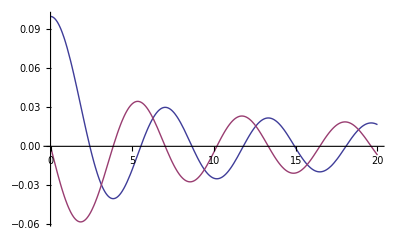

```mathematica
Plot[{m,n},{t,0,20}]
```

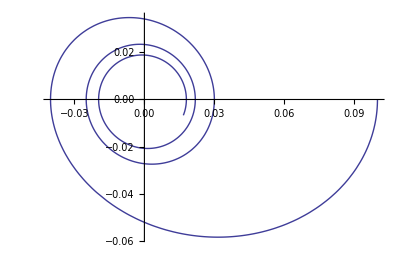

```mathematica
ParametricPlot[{m,n},{t,0,20}]
```

Here, we’ll vary the inital position by pulling around the locator. Then we can watch as the plot spirals toward the eq point at (0,0). Importantly, the spiral becomes more circular over time. The most important outcome of the eigenvalue study is that the Bessel function behaves much like a traditional cosine function at large values of t.

```mathematica
Manipulate[Show[StreamPlot[{f,g}/.{x[t]->x,y[t]->y,t->d,p->0},{x,-5,5},{y,-5,5}],ParametricPlot[Evaluate[{x[t],y[t]}/.Quiet[DSolve[{x'[t]==f,y'[t]==g,x[0]==l[[1]],y[0]==0}/.{p->0},{x[t],y[t]},t]][[1]]],{t,0,d},PlotRange->{-10,40},PlotStyle->{Red,Thick}], PlotLabel->Evaluate[Eigenvalues[co]/.{t->d,p->0}//N]],{{l,{1,1}},Locator},{d,10^-9,30}]
```